Define the components of a density matrix

```mathematica
(Ρ[t_]=({{Subscript[ρ, g,g][t], Subscript[ρ, g,e][t]}, {Subscript[ρ, e,g][t], Subscript[ρ, e,e][t]}}))//MatrixForm
```

(ρ_(g,g)[t] | ρ_(g,e)[t]
ρ_(e,g)[t] | ρ_(e,e)[t])

```mathematica
Commute[A_,B_]:=A.B-B.A;
```

```mathematica
𝒟[A_,ρ_]:=A.ρ.A†-(A†.A.ρ+ρ.A†.A)/2
```

```mathematica
(Z=PauliMatrix[3])//MatrixForm
```

(1 | 0
0 | -1)

```mathematica
-I Commute[ Δ/2 Z,Ρ[t]]//MatrixForm
```

(0 | -ⅈ Δ ρ_(g,e)[t]
ⅈ Δ ρ_(e,g)[t] | 0)

```mathematica
𝒟[Z,Ρ[t]]//MatrixForm
```

(0 | -2 ρ_(g,e)[t]
-2 ρ_(e,g)[t] | 0)

#### Von Neumann equation

Define the von Neumann equation as an object that should be zero

```mathematica
(*0 =*)Ρ'[t]-(-I Commute[ Δ/2 Z,Ρ[t]])//MatrixForm
%//Flatten
```

(ρ_(g,g)'[t] | ⅈ Δ ρ_(g,e)[t]+ρ_(g,e)'[t]
-ⅈ Δ ρ_(e,g)[t]+ρ_(e,g)'[t] | ρ_(e,e)'[t])

{ρ_(g,g)'[t],ⅈ Δ ρ_(g,e)[t]+ρ_(g,e)'[t],-ⅈ Δ ρ_(e,g)[t]+ρ_(e,g)'[t],ρ_(e,e)'[t]}

```mathematica
Flatten[Ρ'[t]]
```

{ρ_(g,g)'[t],ρ_(g,e)'[t],ρ_(e,g)'[t],ρ_(e,e)'[t]}

```mathematica
Flatten[(-I Commute[ Δ/2 Z,Ρ[t]])]
```

{0,-ⅈ Δ ρ_(g,e)[t],ⅈ Δ ρ_(e,g)[t],0}

Define the von Neumann equations componentwise

```mathematica
vNequations=Flatten[Ρ'[t]]==Flatten[(-I Commute[ Δ/2 Z,Ρ[t]])]//Thread
```

{ρ_(g,g)'[t]==0,ρ_(g,e)'[t]==-ⅈ Δ ρ_(g,e)[t],ρ_(e,g)'[t]==ⅈ Δ ρ_(e,g)[t],ρ_(e,e)'[t]==0}

The RHS of the von Neumann equation:

```mathematica
vNRHS=Flatten[(-I Commute[ Δ/2 Z,Ρ[t]])]
```

{0,-ⅈ Δ ρ_(g,e)[t],ⅈ Δ ρ_(e,g)[t],0}

Initial conditions

```mathematica
initequs=Flatten[Ρ[0]]==Flatten[({{a, b}, {c, d}})]//Thread
```

{ρ_(g,g)[0]==a,ρ_(g,e)[0]==b,ρ_(e,g)[0]==c,ρ_(e,e)[0]==d}

Solve the vN equations with Mathematica DSolve

```mathematica
solvN=DSolve[Join[vNequations,initequs],Ρ[t]//Flatten,t][[1]]
```

{ρ_(g,g)[t]→a,ρ_(g,e)[t]→b ⅇ^(-ⅈ t Δ),ρ_(e,g)[t]→c ⅇ^(ⅈ t Δ),ρ_(e,e)[t]→d}

```mathematica
Ρ[t]/.solvN//MatrixForm
%/.t->0//MatrixForm
```

(a | b ⅇ^(-ⅈ t Δ)
c ⅇ^(ⅈ t Δ) | d)

(a | b
c | d)

```mathematica
Normal/@CoefficientArrays[vNRHS,Ρ[t]//Flatten]
```

{{0,0,0,0},{{0,0,0,0},{0,-ⅈ Δ,0,0},{0,0,ⅈ Δ,0},{0,0,0,0}}}

Extract the coefficient matrix representing ρ'[t]=B.ρ[t] as if ρ were a large vector

```mathematica
(B=CoefficientArrays[vNRHS,Ρ[t]//Flatten][[2]])//MatrixForm
```

(0 | 0 | 0 | 0
0 | -ⅈ Δ | 0 | 0
0 | 0 | ⅈ Δ | 0
0 | 0 | 0 | 0)

```mathematica
vNRHS==B.(Ρ[t]//Flatten)
```

True

Solve the vectorised form of the von Neumann equation

```mathematica
MatrixExp[B t].(Ρ[0]//Flatten)
```

{ρ_(g,g)[0],ⅇ^(-ⅈ t Δ) ρ_(g,e)[0],ⅇ^(ⅈ t Δ) ρ_(e,g)[0],ρ_(e,e)[0]}

Compare with the first solution

```mathematica
sol
```

{ρ_(g,g)[t]→a,ρ_(g,e)[t]→b ⅇ^(-ⅈ t Δ),ρ_(e,g)[t]→c ⅇ^(ⅈ t Δ),ρ_(e,e)[t]→d}

#### Lindblad master

Now add the dissipator to get a Lindblad equation:

```mathematica
(*0 =*)Ρ'[t]-(-I Commute[ Δ/2 Z,Ρ[t]]+γ 𝒟[Z/2,Ρ[t]])//MatrixForm
%//Flatten
```

(ρ_(g,g)'[t] | 1/2 γ ρ_(g,e)[t]+ⅈ Δ ρ_(g,e)[t]+ρ_(g,e)'[t]
1/2 γ ρ_(e,g)[t]-ⅈ Δ ρ_(e,g)[t]+ρ_(e,g)'[t] | ρ_(e,e)'[t])

{ρ_(g,g)'[t],1/2 γ ρ_(g,e)[t]+ⅈ Δ ρ_(g,e)[t]+ρ_(g,e)'[t],1/2 γ ρ_(e,g)[t]-ⅈ Δ ρ_(e,g)[t]+ρ_(e,g)'[t],ρ_(e,e)'[t]}

```mathematica
LMequations=Flatten[Ρ'[t]-(-I Commute[ Δ/2 Z,Ρ[t]]+γ 𝒟[Z/2,Ρ[t]])]==0//Thread
```

{ρ_(g,g)'[t]==0,1/2 γ ρ_(g,e)[t]+ⅈ Δ ρ_(g,e)[t]+ρ_(g,e)'[t]==0,1/2 γ ρ_(e,g)[t]-ⅈ Δ ρ_(e,g)[t]+ρ_(e,g)'[t]==0,ρ_(e,e)'[t]==0}

```mathematica
LMERHS=Flatten[(-I Commute[ Δ/2 Z,Ρ[t]]+γ 𝒟[Z/2,Ρ[t]])]
```

{0,-1/2 γ ρ_(g,e)[t]-ⅈ Δ ρ_(g,e)[t],-1/2 γ ρ_(e,g)[t]+ⅈ Δ ρ_(e,g)[t],0}

```mathematica
(BLME=CoefficientArrays[LMERHS,Ρ[t]//Flatten][[2]])//MatrixForm
```

(0 | 0 | 0 | 0
0 | -γ/2-ⅈ Δ | 0 | 0
0 | 0 | -γ/2+ⅈ Δ | 0
0 | 0 | 0 | 0)

```mathematica
BLME+BLME†//Normal//FullSimplify[#,γ∈Reals&&Δ∈Reals]&//MatrixForm
```

(0 | 0 | 0 | 0
0 | -γ | 0 | 0
0 | 0 | -γ | 0
0 | 0 | 0 | 0)

```mathematica
MatrixExp[BLME t]
%.Flatten[Ρ[0]]//Simplify
```

{{1,0,0,0},{0,ⅇ^(-1/2 t (γ+2 ⅈ Δ)),0,0},{0,0,ⅇ^(-1/2 t (γ-2 ⅈ Δ)),0},{0,0,0,1}}

{ρ_(g,g)[0],ⅇ^(-1/2 t (γ+2 ⅈ Δ)) ρ_(g,e)[0],ⅇ^(-1/2 t (γ-2 ⅈ Δ)) ρ_(e,g)[0],ρ_(e,e)[0]}

```mathematica
solvN
```

{ρ_(g,g)[t]→a,ρ_(g,e)[t]→b ⅇ^(-ⅈ t Δ),ρ_(e,g)[t]→c ⅇ^(ⅈ t Δ),ρ_(e,e)[t]→d}

```mathematica
solLM=DSolve[Join[LMequations,initequs],Ρ[t]//Flatten,t][[1]]
```

{ρ_(g,g)[t]→a,ρ_(g,e)[t]→b ⅇ^(-(t γ)/2-ⅈ t Δ),ρ_(e,g)[t]→c ⅇ^(-(t γ)/2+ⅈ t Δ),ρ_(e,e)[t]→d}

```mathematica
solvN/.t->0
solLM/.t->0
```

{ρ_(g,g)[0]→a,ρ_(g,e)[0]→b,ρ_(e,g)[0]→c,ρ_(e,e)[0]→d}

{ρ_(g,g)[0]→a,ρ_(g,e)[0]→b,ρ_(e,g)[0]→c,ρ_(e,e)[0]→d}

```mathematica
Ρ[t]/.solvN//MatrixForm
```

(a | b ⅇ^(-ⅈ t Δ)
c ⅇ^(ⅈ t Δ) | d)

```mathematica
Ρ[t]/.solLM//MatrixForm
```

(a | b ⅇ^(-(t γ)/2-ⅈ t Δ)
c ⅇ^(-(t γ)/2+ⅈ t Δ) | d)

The off-diagonal coherences oscillate.  The closed evolution is cosine oscillation indefinitely; the open systems evolution has decaying oscillations:

{1/2 Cos[t Δ],1/2 ⅇ^(-(t γ)/2) Cos[t Δ]}

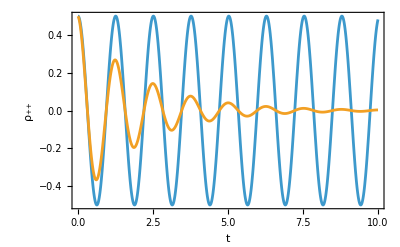

```mathematica
(Subscript[ρ, e,g][t]+Subscript[ρ, g,e][t])/2/.{solvN,solLM}/.{b->1/2,c->1/2}//FullSimplify[#,Δ>0&&γ>0&&t>0]&
Plot[Evaluate[%/.{γ->1,Δ->5}],{t,0,10},PlotRange->All,Frame->True,FrameLabel->{t,Subscript[ρ, "++"]}]
```